## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = False;
removeOutputFiles = False;

rxnName="FBP2";
fitLabel=rxnName;
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;
(*Q10 Correction Options*)
Q10KcatCorrectionFlag = True (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)


(* user will need to change this path *)
pathMASSef = "/home/mrama/Dropbox/test bla/MASSef/";
kineticDataFileName =  "kinetic_data_model.csv";

mainFolder = "fit_FBP2";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

True

Working dir:/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName, assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological];
```

(fdp^c+h2o^c→f6p^c+pi^c)^FBP2

;

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp,Null | 41.5 | 39.425
43.575 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp | 0.00007 | 0.000068
0.000072 |  | M | 9 | 37 | chesk | 0.5 | mn2 | 0.002
cl | 0.004

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp | Null | 5.7 | 5.6
5.8 | 1/s | 9 | 37 | chesk | 0.5 | mn2 | 0.002
cl | 0.004
1 | fdp | 0.00006
pep | 0.001 | 9.66905 | 9.1856
10.1525 | 1/s | 7.7 | 37 | tric | 0.02 | mn2 | 0.001
cl | 0.002
1 | fdp | 0.00005
atp | 0.00125 | 5.01469 | 4.76396
5.26543 | 1/s | 7.7 | 37 | tric | 0.02 | mn2 | 0.001
1 | fdp | 0.00005
adp | 0.00125 | 2.84967 | 2.70718
2.99215 | 1/s | 7.7 | 37 | tric | 0.02 | mn2 | 0.001
1 | fdp | 0.00005
adp | 0.0019 | 2.16202 | 2.05392
2.27013 | 1/s | 7.7 | 37 | tric | 0.02 | mn2 | 0.001

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Kic | f1p | 0.001 | 0.00095
0.00105 |  | Competitive | fdp | 0.00007 | M | 7.7 | 25 | tric | 0.02 | mn2 | 0.001
cl | 0.002
1 | Kic | pi | 0.00035 | 0.0003325
0.0003675 |  | Competitive | fdp | 0.00007 | M | 7.7 | 25 | tric | 0.02 | mn2 | 0.001
cl | 0.002

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | n | fdp | 2 | 2.
2.1 |  |  | 9 | 37 | chesk | 0.5 | mn2 | 0.002
cl | 0.004

### Define data points priority (optional)

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {1};
kmPriorities = {};
s05Priorities = {1};
kcatPriorities = {1,1,0,1,0};
inhibitionPriorities={0,0};
activationPriorities = Null;
otherParamsPriorities = {1};


{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

(fdp^c+h2o^c→f6p^c+pi^c)^FBP2

;

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp,Null | 41.5 | 39.425
43.575 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp | 0.00007 | 0.000068
0.000072 |  | M | 9 | 37 | chesk | 0.5 | mn2 | 0.002
cl | 0.004

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp | Null | 5.7 | 5.6
5.8 | 1/s | 9 | 37 | chesk | 0.5 | mn2 | 0.002
cl | 0.004
1 | fdp | 0.00006
pep | 0.001 | 9.66905 | 9.1856
10.1525 | 1/s | 7.7 | 37 | tric | 0.02 | mn2 | 0.001
cl | 0.002
1 | fdp | 0.00005
adp | 0.00125 | 2.84967 | 2.70718
2.99215 | 1/s | 7.7 | 37 | tric | 0.02 | mn2 | 0.001

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | n | fdp | 2 | 2.
2.1 |  |  | 9 | 37 | chesk | 0.5 | mn2 | 0.002
cl | 0.004

## Construct Module and Set Up Comparison Equations

### Construct enzyme module

```mathematica
enz ="E_FBP2[c]"
substrateList ={"fdp"};
productList={"pi", "f6p"};
nActiveSites = 2;
bindingReversibility = " <=> ";
releaseReversibility = " <=> ";
transitionReversibility = "<=> ";

catalyticBranch =generateOrderedMechanism[enz, substrateList,  productList, nActiveSites, bindingReversibility, 
						transitionReversibility, releaseReversibility] ;

enzymeModelOrig=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{m["pep","c"], m["adp","c"]},ActivationSites->1,Inhibitors->{},InhibitionSites->1];

catalyticBranch//TableForm
enzymeModelOrig["Reactions"]
```

E_FBP2[c]

E_FBP2[c] + fdp[c] <=> E_FBP2[c]&fdp
E_FBP2[c]&fdp + fdp[c] <=> E_FBP2[c]&fdp&fdp
E_FBP2[c]&fdp&fdp<=> E_FBP2[c]&pi&pi&f6p&f6p
E_FBP2[c]&pi&pi&f6p&f6p <=> E_FBP2[c]&pi&pi&f6p + f6p[c]
E_FBP2[c]&pi&pi&f6p <=> E_FBP2[c]&pi&pi + f6p[c]
E_FBP2[c]&pi&pi <=> E_FBP2[c]&pi + pi[c]
E_FBP2[c]&pi <=> E_FBP2[c] + pi[c]

```mathematica
catalyticBranch={"E_FBP2[c] + fdp[c] <=> E_FBP2[c]&fdp",
				"E_FBP2[c]&fdp + fdp[c] <=> E_FBP2[c]&fdp&fdp",
				"E_FBP2[c]&fdp&fdp <=> E_FBP2[c]&f6p&f6p&pi&pi",		
			        "E_FBP2[c]&f6p&f6p&pi&pi <=> E_FBP2[c]&f6p&f6p&pi + pi[c]",
				"E_FBP2[c]&f6p&f6p&pi <=> E_FBP2[c]&f6p&f6p + pi[c]",
				"E_FBP2[c]&f6p&f6p<=> E_FBP2[c]&f6p+ f6p[c]",
				"E_FBP2[c]&f6p <=> E_FBP2[c] + f6p[c]",
				
				"E_FBP2[c] + pep[c] <=> E_FBP2[c]&pep",
				"E_FBP2[c]&pep + fdp[c] <=> E_FBP2[c]&pep&fdp",
				"E_FBP2[c]&pep&fdp + fdp[c] <=> E_FBP2[c]&pep&fdp&fdp",
				"E_FBP2[c]&pep&fdp&fdp<=> E_FBP2[c]&pep&f6p&f6p&pi&pi",
				"E_FBP2[c]&pep&f6p&f6p&pi&pi <=> E_FBP2[c]&pep&f6p&f6p&pi  + pi[c]",
				"E_FBP2[c]&pep&f6p&f6p&pi <=> E_FBP2[c]&pep&f6p&f6p + pi[c]",
				"E_FBP2[c]&pep&f6p&f6p <=> E_FBP2[c]&pep&f6p + f6p[c]",
				"E_FBP2[c]&pep&f6p <=> E_FBP2[c]&pep + f6p[c]",
		

				"E_FBP2[c] + adp[c] <=> E_FBP2[c]&adp",
				"E_FBP2[c]&adp + fdp[c] <=> E_FBP2[c]&adp&fdp",
				"E_FBP2[c]&adp&fdp + fdp[c] <=> E_FBP2[c]&adp&fdp&fdp",
				"E_FBP2[c]&adp&fdp&fdp <=> E_FBP2[c]&adp&f6p&f6p&pi&pi",
				"E_FBP2[c]&adp&f6p&f6p&pi&pi <=> E_FBP2[c]&adp&f6p&f6p&pi + pi[c]",
				"E_FBP2[c]&adp&f6p&f6p&pi <=> E_FBP2[c]&adp&f6p&f6p + pi[c]",
				"E_FBP2[c]&adp&f6p&f6p <=> E_FBP2[c]&adp&f6p + f6p[c]",
				"E_FBP2[c]&adp&f6p <=> E_FBP2[c]&adp + f6p[c]"};

			
enzymeModelOrig=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];


enzymeModelOrig["Reactions"]
```

{((FBP2^c)_^+adp^c⇌(FBP2^c&adp^c)_^)^FBP21,((FBP2^c)_^+pep^c⇌(FBP2^c&pep^c)_^)^FBP22,((FBP2^c)_^+fdp^c⇌(FBP2^c&fdp^c)_^)^FBP23,((FBP2^c&adp^c)_^+fdp^c⇌(FBP2^c&adp^c&fdp^c)_^)^FBP24,((FBP2^c&pep^c)_^+fdp^c⇌(FBP2^c&pep^c&fdp^c)_^)^FBP25,((FBP2^c&f6p^c)_^⇌(FBP2^c)_^+f6p^c)^FBP26,((FBP2^c&fdp^c)_^+fdp^c⇌(FBP2^c&fdp^c&fdp^c)_^)^FBP27,((FBP2^c&adp^c&f6p^c)_^⇌(FBP2^c&adp^c)_^+f6p^c)^FBP28,((FBP2^c&adp^c&fdp^c)_^+fdp^c⇌(FBP2^c&adp^c&fdp^c&fdp^c)_^)^FBP29,((FBP2^c&pep^c&f6p^c)_^⇌(FBP2^c&pep^c)_^+f6p^c)^FBP210,((FBP2^c&pep^c&fdp^c)_^+fdp^c⇌(FBP2^c&pep^c&fdp^c&fdp^c)_^)^FBP211,((FBP2^c&f6p^c&f6p^c)_^⇌(FBP2^c&f6p^c)_^+f6p^c)^FBP212,((FBP2^c&fdp^c&fdp^c)_^⇌(FBP2^c&f6p^c&f6p^c&pi^c&pi^c)_^)^FBP213,((FBP2^c&adp^c&f6p^c&f6p^c)_^⇌(FBP2^c&adp^c&f6p^c)_^+f6p^c)^FBP214,((FBP2^c&adp^c&fdp^c&fdp^c)_^⇌(FBP2^c&adp^c&f6p^c&f6p^c&pi^c&pi^c)_^)^FBP215,((FBP2^c&pep^c&f6p^c&f6p^c)_^⇌(FBP2^c&pep^c&f6p^c)_^+f6p^c)^FBP216,((FBP2^c&pep^c&fdp^c&fdp^c)_^⇌(FBP2^c&pep^c&f6p^c&f6p^c&pi^c&pi^c)_^)^FBP217,((FBP2^c&f6p^c&f6p^c&pi^c)_^⇌(FBP2^c&f6p^c&f6p^c)_^+pi^c)^FBP218,((FBP2^c&adp^c&f6p^c&f6p^c&pi^c)_^⇌(FBP2^c&adp^c&f6p^c&f6p^c)_^+pi^c)^FBP219,((FBP2^c&pep^c&f6p^c&f6p^c&pi^c)_^⇌(FBP2^c&pep^c&f6p^c&f6p^c)_^+pi^c)^FBP220,((FBP2^c&f6p^c&f6p^c&pi^c&pi^c)_^⇌(FBP2^c&f6p^c&f6p^c&pi^c)_^+pi^c)^FBP221,((FBP2^c&adp^c&f6p^c&f6p^c&pi^c&pi^c)_^⇌(FBP2^c&adp^c&f6p^c&f6p^c&pi^c)_^+pi^c)^FBP222,((FBP2^c&pep^c&f6p^c&f6p^c&pi^c&pi^c)_^⇌(FBP2^c&pep^c&f6p^c&f6p^c&pi^c)_^+pi^c)^FBP223}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1={((FBP2^c)_^+fdp^c⇌(FBP2^c&fdp^c)_^)^FBP23,Overscript[(FBP2^c&f6p^c)_^⇌(FBP2^c)_^+f6p^c, FBP26],((FBP2^c&fdp^c)_^+fdp^c⇌(FBP2^c&fdp^c&fdp^c)_^)^FBP27,Overscript[(FBP2^c&f6p^c&f6p^c)_^⇌(FBP2^c&f6p^c)_^+f6p^c, FBP212],((FBP2^c&fdp^c&fdp^c)_^⇌(FBP2^c&f6p^c&f6p^c&pi^c&pi^c)_^)^FBP213,Overscript[(FBP2^c&f6p^c&f6p^c&pi^c)_^⇌(FBP2^c&f6p^c&f6p^c)_^+pi^c, FBP218],Overscript[(FBP2^c&f6p^c&f6p^c&pi^c&pi^c)_^⇌(FBP2^c&f6p^c&f6p^c&pi^c)_^+pi^c, FBP221]};
catalyticReactionsSet2={((FBP2^c&adp^c)_^+fdp^c⇌(FBP2^c&adp^c&fdp^c)_^)^FBP24,Overscript[(FBP2^c&adp^c&f6p^c)_^⇌(FBP2^c&adp^c)_^+f6p^c, FBP28],((FBP2^c&adp^c&fdp^c)_^+fdp^c⇌(FBP2^c&adp^c&fdp^c&fdp^c)_^)^FBP29,Overscript[(FBP2^c&adp^c&f6p^c&f6p^c)_^⇌(FBP2^c&adp^c&f6p^c)_^+f6p^c, FBP214],((FBP2^c&adp^c&fdp^c&fdp^c)_^⇌(FBP2^c&adp^c&f6p^c&f6p^c&pi^c&pi^c)_^)^FBP215,Overscript[(FBP2^c&adp^c&f6p^c&f6p^c&pi^c)_^⇌(FBP2^c&adp^c&f6p^c&f6p^c)_^+pi^c, FBP219],Overscript[(FBP2^c&adp^c&f6p^c&f6p^c&pi^c&pi^c)_^⇌(FBP2^c&adp^c&f6p^c&f6p^c&pi^c)_^+pi^c, FBP222]};
catalyticReactionsSet3={((FBP2^c&pep^c)_^+fdp^c⇌(FBP2^c&pep^c&fdp^c)_^)^FBP25,Overscript[(FBP2^c&pep^c&f6p^c)_^⇌(FBP2^c&pep^c)_^+f6p^c, FBP210],((FBP2^c&pep^c&fdp^c)_^+fdp^c⇌(FBP2^c&pep^c&fdp^c&fdp^c)_^)^FBP211,Overscript[(FBP2^c&pep^c&f6p^c&f6p^c)_^⇌(FBP2^c&pep^c&f6p^c)_^+f6p^c, FBP216],((FBP2^c&pep^c&fdp^c&fdp^c)_^⇌(FBP2^c&pep^c&f6p^c&f6p^c&pi^c&pi^c)_^)^FBP217,Overscript[(FBP2^c&pep^c&f6p^c&f6p^c&pi^c)_^⇌(FBP2^c&pep^c&f6p^c&f6p^c)_^+pi^c, FBP220],Overscript[(FBP2^c&pep^c&f6p^c&f6p^c&pi^c&pi^c)_^⇌(FBP2^c&pep^c&f6p^c&f6p^c&pi^c)_^+pi^c, FBP223]};(*

catalyticReactionsSet1={((FBP2^c)_^+fdp^c⇌(FBP2^c&fdp^c)_^)^FBP22((FBP2^c&f6p^c)_^⇌(FBP2^c)_^+f6p^c)^FBP24,((FBP2^c&fdp^c)_^+fdp^c⇌(FBP2^c&fdp^c&fdp^c)_^)^FBP25,((FBP2^c&f6p^c&f6p^c)_^⇌(FBP2^c&f6p^c)_^+f6p^c)^FBP28,((FBP2^c&fdp^c&fdp^c)_^⇌(FBP2^c&f6p^c&f6p^c&pi^c&pi^c)_^)^FBP29,((FBP2^c&f6p^c&f6p^c&pi^c)_^⇌(FBP2^c&f6p^c&f6p^c)_^+pi^c)^FBP212,((FBP2^c&f6p^c&f6p^c&pi^c&pi^c)_^⇌(FBP2^c&f6p^c&f6p^c&pi^c)_^+pi^c)^FBP214};
catalyticReactionsSet2={((FBP2^c&adp^c)_^+fdp^c⇌(FBP2^c&adp^c&fdp^c)_^)^FBP23,((FBP2^c&adp^c&f6p^c)_^⇌(FBP2^c&adp^c)_^+f6p^c)^FBP26,((FBP2^c&adp^c&fdp^c)_^+fdp^c⇌(FBP2^c&adp^c&fdp^c&fdp^c)_^)^FBP27,((FBP2^c&adp^c&f6p^c&f6p^c)_^⇌(FBP2^c&adp^c&f6p^c)_^+f6p^c)^FBP210,((FBP2^c&adp^c&fdp^c&fdp^c)_^⇌(FBP2^c&adp^c&f6p^c&f6p^c&pi^c&pi^c)_^)^FBP211,((FBP2^c&adp^c&f6p^c&f6p^c&pi^c)_^⇌(FBP2^c&adp^c&f6p^c&f6p^c)_^+pi^c)^FBP213,((FBP2^c&adp^c&f6p^c&f6p^c&pi^c&pi^c)_^⇌(FBP2^c&adp^c&f6p^c&f6p^c&pi^c)_^+pi^c)^FBP215};*)

catalyticReactionsSetsList = {catalyticReactionsSet1,catalyticReactionsSet2,catalyticReactionsSet3};
```

### Setup King-Altman Equations

```mathematica
getRateEqsLocal[rxn_, enzymeModel_, absoluteFlux_, rateConstSubstitutionList_, rateConstSubstitutionList2_, reverseZeroSub_, 
		   forwardZeroSub_, volumeSub_, metSatForSubList_, metSatRevSubList_,
		   outputPath_,  absoluteFluxRelRateFor_:Null, absoluteFluxRelRateRev_:Null, 
		   otherMetsForwardZeroSub_:Null, otherMetsReverseZeroSub_:Null,
		   simplifyFlag_:True, simplifyMaxTime_:300]:= 
	Block[{absoluteFluxEqn, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse,
			absoluteRateEqRelRateFor, absoluteRateEqRelRateRev, absoluteFluxEqRelRateFor, absoluteFluxEqRelRateRev,
			otherRelativeRatesForward={}, otherRelativeRatesReverse={},
			posConcentrationAssumption, rateFileName, rateEq, repeatedMetCount, e, s},
			
	absoluteFluxEqn = absoluteFlux[[2]]/.rateConstSubstitutionList/.rateConstSubstitutionList2;(* Equivalent Rate Constants *)

	posConcentrationAssumption = Map[# >= 0. &, enzymeModel["Species"]];
	
	s = AbsoluteTime[];
	
	(*kcat Forward*)
	rateFileName = FileNameJoin[{outputPath, "absRateFor.m"}, OperatingSystem->$OperatingSystem];
	absoluteRateForward = 
		If[! FileExistsQ[rateFileName], (* if file with absRateFor doesnt exist, create it *)
			Print["Generating absolute rate forward equation..."];
			If[TrueQ[simplifyFlag],
				Print["Simplifying..."];
				rateEq = anonymize[Simplify[(absoluteFluxEqn/.reverseZeroSub/.volumeSub), TimeConstraint->simplifyMaxTime, Trig->False, Assumptions->posConcentrationAssumption]];,
				rateEq = (absoluteFluxEqn/.reverseZeroSub/.volumeSub);	
			];
			Export[rateFileName, rateEq];
			rateEq,
			
			Print["Loading absolute rate forward equation..."];
			Import[rateFileName]
		];
	
	e = AbsoluteTime[];
	Print[e-s];

	
	s = AbsoluteTime[];
	(*Forward Km(s)*)
	relativeRateForward = 
		Table[
			rateFileName = FileNameJoin[{outputPath, "relRateFor_"<> getID@Keys[metSatForSub] <> ".m"}, OperatingSystem->$OperatingSystem]; 
				rateEq = anonymize[Simplify[absoluteRateForward/(Limit[absoluteRateForward, metSatForSub]), TimeConstraint->simplifyMaxTime, Trig->False, Assumptions->posConcentrationAssumption]];
				Export[rateFileName, rateEq];
				rateEq,
		{metSatForSub, metSatForSubList}];

	e = AbsoluteTime[];
	Print[e-s];
	

	
	Which[
		(otherMetsForwardZeroSub === Null || otherMetsForwardZeroSub === {}) && (otherMetsReverseZeroSub === Null || otherMetsReverseZeroSub === {}),
		Return[{absoluteRateForward, 0, relativeRateForward, {0,0}, Null, Null}],
		
		(otherMetsForwardZeroSub === Null || otherMetsForwardZeroSub === {}) && !(otherMetsReverseZeroSub === Null || otherMetsReverseZeroSub === {}),
		Return[{absoluteRateForward, 0, relativeRateForward,  {0,0}, Flatten[otherRelativeRatesForward,1], Null}],
		
		!(otherMetsForwardZeroSub === Null || otherMetsForwardZeroSub === {}) && (otherMetsReverseZeroSub === Null || otherMetsReverseZeroSub === {}),
		Return[{absoluteRateForward, 0, relativeRateForward,  {0,0}, Null, Flatten[otherRelativeRatesReverse,1]}],
		
		!(otherMetsForwardZeroSub === Null || otherMetsForwardZeroSub === {}) && !(otherMetsReverseZeroSub === Null || otherMetsReverseZeroSub === {}),
		Return[{absoluteRateForward, 0, relativeRateForward,  {0,0}, Flatten[otherRelativeRatesForward,1], Flatten[otherRelativeRatesReverse,1]}]
	];
];
```

```mathematica
metList = Cases[enzymeModelOrig["Species"], _metabolite];
    enzFormList=Cases[enzymeModelOrig["Species"], _enzyme];

	res = Table[
					

						Table[
				
						Which[Length[Cases[getSubstrates[rxn],_metabolite]] > 0 &&SameQ[Cases[getSubstrates[rxn],_metabolite][[1]], met] ,
							rxn,
		
							Length[Cases[getProducts[rxn],_metabolite]] > 0 &&SameQ[Cases[getProducts[rxn],_metabolite][[1]], met],
						rxn
						],

						{rxn, enzymeModelOrig["Reactions"]}],
	
				{met, metList}];
```

```mathematica
res2 = Map[Flatten@DeleteCases[#, Null]&, res];
```

```mathematica
metList = Cases[enzymeModelOrig["Species"], _metabolite];
    enzFormList=Cases[enzymeModelOrig["Species"], _enzyme];

	res3 =Table[ 
		Table[
					
					boundMets=DeleteDuplicates@getCatalytic[enzForm];
						Table[
					
						Which[SameQ[DeleteDuplicates@getCatalytic[Cases[getSubstrates[rxn],_enzyme][[1]]], boundMets],
					
							{rateconst[getID[rxn], True], rateconst[getID[rxn], False]},
		
							SameQ[DeleteDuplicates@getCatalytic[Cases[getProducts[rxn],_enzyme][[1]]], boundMets],
					
							{rateconst[getID[rxn], True], rateconst[getID[rxn], False]}
						],

						{rxn, rxnGroup}],
	
				{enzForm, enzFormList}],
{rxnGroup, res2}];
```

```mathematica
DeleteDuplicates@ DeleteCases[Map[Flatten@DeleteCases[#, Null]&,Flatten[res3,1]],{}]
```

{{k_FBP26^⟶,k_FBP26^⟵},{k_FBP28^⟶,k_FBP28^⟵},{k_FBP26^⟶,k_FBP26^⟵,k_FBP212^⟶,k_FBP212^⟵},{k_FBP210^⟶,k_FBP210^⟵},{k_FBP28^⟶,k_FBP28^⟵,k_FBP214^⟶,k_FBP214^⟵},{k_FBP210^⟶,k_FBP210^⟵,k_FBP216^⟶,k_FBP216^⟵},{k_FBP23^⟶,k_FBP23^⟵},{k_FBP24^⟶,k_FBP24^⟵},{k_FBP23^⟶,k_FBP23^⟵,k_FBP27^⟶,k_FBP27^⟵},{k_FBP25^⟶,k_FBP25^⟵},{k_FBP24^⟶,k_FBP24^⟵,k_FBP29^⟶,k_FBP29^⟵},{k_FBP25^⟶,k_FBP25^⟵,k_FBP211^⟶,k_FBP211^⟵},{k_FBP22^⟶,k_FBP22^⟵},{k_FBP218^⟶,k_FBP218^⟵},{k_FBP219^⟶,k_FBP219^⟵},{k_FBP220^⟶,k_FBP220^⟵},{k_FBP218^⟶,k_FBP218^⟵,k_FBP221^⟶,k_FBP221^⟵},{k_FBP219^⟶,k_FBP219^⟵,k_FBP222^⟶,k_FBP222^⟵},{k_FBP220^⟶,k_FBP220^⟵,k_FBP223^⟶,k_FBP223^⟵},{k_FBP21^⟶,k_FBP21^⟵}}

```mathematica
rateConstSub={{Subscript[k, FBP24]^⟶,Subscript[k, FBP24]^⟵,Subscript[k, FBP28]^⟶,Subscript[k, FBP28]^⟵},{Subscript[k, FBP26]^⟶,Subscript[k, FBP26]^⟵,Subscript[k, FBP210]^⟶,Subscript[k, FBP210]^⟵},{Subscript[k, FBP22]^⟶,Subscript[k, FBP22]^⟵,Subscript[k, FBP25]^⟶,Subscript[k, FBP25]^⟵},{Subscript[k, FBP23]^⟶,Subscript[k, FBP23]^⟵,Subscript[k, FBP27]^⟶,Subscript[k, FBP27]^⟵},{Subscript[k, FBP212]^⟶,Subscript[k, FBP212]^⟵,Subscript[k, FBP214]^⟶,Subscript[k, FBP214]^⟵},{Subscript[k, FBP213]^⟶,Subscript[k, FBP213]^⟵,Subscript[k, FBP215]^⟶,Subscript[k, FBP215]^⟵}};
```

```mathematica
rateConstSub = Table[Print@ratesGroup;

					{Map[#-> ratesGroup[[1]]&, ratesGroup[[1;; Length@ratesGroup;; 2]]],
						Map[#-> ratesGroup[[2]]&, ratesGroup[[2;; Length@ratesGroup;; 2]]]},

					{ratesGroup, rateConstSub}] // Flatten;
```

{k_FBP24^⟶,k_FBP24^⟵,k_FBP28^⟶,k_FBP28^⟵}

{k_FBP26^⟶,k_FBP26^⟵,k_FBP210^⟶,k_FBP210^⟵}

{k_FBP22^⟶,k_FBP22^⟵,k_FBP25^⟶,k_FBP25^⟵}

{k_FBP23^⟶,k_FBP23^⟵,k_FBP27^⟶,k_FBP27^⟵}

{k_FBP212^⟶,k_FBP212^⟵,k_FBP214^⟶,k_FBP214^⟵}

{k_FBP213^⟶,k_FBP213^⟵,k_FBP215^⟶,k_FBP215^⟵}

```mathematica
rateConstSub
```

{k_FBP24^⟶→k_FBP24^⟶,k_FBP28^⟶→k_FBP24^⟶,k_FBP24^⟵→k_FBP24^⟵,k_FBP28^⟵→k_FBP24^⟵,k_FBP26^⟶→k_FBP26^⟶,k_FBP210^⟶→k_FBP26^⟶,k_FBP26^⟵→k_FBP26^⟵,k_FBP210^⟵→k_FBP26^⟵,k_FBP22^⟶→k_FBP22^⟶,k_FBP25^⟶→k_FBP22^⟶,k_FBP22^⟵→k_FBP22^⟵,k_FBP25^⟵→k_FBP22^⟵,k_FBP23^⟶→k_FBP23^⟶,k_FBP27^⟶→k_FBP23^⟶,k_FBP23^⟵→k_FBP23^⟵,k_FBP27^⟵→k_FBP23^⟵,k_FBP212^⟶→k_FBP212^⟶,k_FBP214^⟶→k_FBP212^⟶,k_FBP212^⟵→k_FBP212^⟵,k_FBP214^⟵→k_FBP212^⟵,k_FBP213^⟶→k_FBP213^⟶,k_FBP215^⟶→k_FBP213^⟶,k_FBP213^⟵→k_FBP213^⟵,k_FBP215^⟵→k_FBP213^⟵}

```mathematica
rateConstSub={Subscript[k, FBP26]^⟶->Subscript[k, FBP26]^⟶,Subscript[k, FBP212]^⟶->Subscript[k, FBP26]^⟶,Subscript[k, FBP26]^⟵->Subscript[k, FBP26]^⟵,Subscript[k, FBP212]^⟵->Subscript[k, FBP26]^⟵,Subscript[k, FBP28]^⟶->Subscript[k, FBP28]^⟶,Subscript[k, FBP214]^⟶->Subscript[k, FBP28]^⟶,Subscript[k, FBP28]^⟵->Subscript[k, FBP28]^⟵,Subscript[k, FBP214]^⟵->Subscript[k, FBP28]^⟵,Subscript[k, FBP210]^⟶->Subscript[k, FBP210]^⟶,Subscript[k, FBP216]^⟶->Subscript[k, FBP210]^⟶,Subscript[k, FBP210]^⟵->Subscript[k, FBP210]^⟵,Subscript[k, FBP216]^⟵->Subscript[k, FBP210]^⟵,Subscript[k, FBP23]^⟶->Subscript[k, FBP23]^⟶,Subscript[k, FBP27]^⟶->Subscript[k, FBP23]^⟶,Subscript[k, FBP23]^⟵->Subscript[k, FBP23]^⟵,Subscript[k, FBP27]^⟵->Subscript[k, FBP23]^⟵,Subscript[k, FBP24]^⟶->Subscript[k, FBP24]^⟶,Subscript[k, FBP29]^⟶->Subscript[k, FBP24]^⟶,Subscript[k, FBP24]^⟵->Subscript[k, FBP24]^⟵,Subscript[k, FBP29]^⟵->Subscript[k, FBP24]^⟵,Subscript[k, FBP25]^⟶->Subscript[k, FBP25]^⟶,Subscript[k, FBP211]^⟶->Subscript[k, FBP25]^⟶,Subscript[k, FBP25]^⟵->Subscript[k, FBP25]^⟵,Subscript[k, FBP211]^⟵->Subscript[k, FBP25]^⟵,Subscript[k, FBP218]^⟶->Subscript[k, FBP218]^⟶,Subscript[k, FBP221]^⟶->Subscript[k, FBP218]^⟶,Subscript[k, FBP218]^⟵->Subscript[k, FBP218]^⟵,Subscript[k, FBP221]^⟵->Subscript[k, FBP218]^⟵,Subscript[k, FBP219]^⟶->Subscript[k, FBP219]^⟶,Subscript[k, FBP222]^⟶->Subscript[k, FBP219]^⟶,Subscript[k, FBP219]^⟵->Subscript[k, FBP219]^⟵,Subscript[k, FBP222]^⟵->Subscript[k, FBP219]^⟵,Subscript[k, FBP220]^⟶->Subscript[k, FBP220]^⟶,Subscript[k, FBP223]^⟶->Subscript[k, FBP220]^⟶,Subscript[k, FBP220]^⟵->Subscript[k, FBP220]^⟵,Subscript[k, FBP223]^⟵->Subscript[k, FBP220]^⟵};
```

```mathematica
rateConstSub={Subscript[k, FBP24]^⟶->Subscript[k, FBP24]^⟶,Subscript[k, FBP28]^⟶->Subscript[k, FBP24]^⟶,Subscript[k, FBP24]^⟵->Subscript[k, FBP24]^⟵,Subscript[k, FBP28]^⟵->Subscript[k, FBP24]^⟵,Subscript[k, FBP26]^⟶->Subscript[k, FBP26]^⟶,Subscript[k, FBP210]^⟶->Subscript[k, FBP26]^⟶,Subscript[k, FBP26]^⟵->Subscript[k, FBP26]^⟵,Subscript[k, FBP210]^⟵->Subscript[k, FBP26]^⟵,Subscript[k, FBP22]^⟶->Subscript[k, FBP22]^⟶,Subscript[k, FBP25]^⟶->Subscript[k, FBP22]^⟶,Subscript[k, FBP22]^⟵->Subscript[k, FBP22]^⟵,Subscript[k, FBP25]^⟵->Subscript[k, FBP22]^⟵,Subscript[k, FBP23]^⟶->Subscript[k, FBP23]^⟶,Subscript[k, FBP27]^⟶->Subscript[k, FBP23]^⟶,Subscript[k, FBP23]^⟵->Subscript[k, FBP23]^⟵,Subscript[k, FBP27]^⟵->Subscript[k, FBP23]^⟵,Subscript[k, FBP212]^⟶->Subscript[k, FBP212]^⟶,Subscript[k, FBP214]^⟶->Subscript[k, FBP212]^⟶,Subscript[k, FBP212]^⟵->Subscript[k, FBP212]^⟵,Subscript[k, FBP214]^⟵->Subscript[k, FBP212]^⟵,Subscript[k, FBP213]^⟶->Subscript[k, FBP213]^⟶,Subscript[k, FBP215]^⟶->Subscript[k, FBP213]^⟶,Subscript[k, FBP213]^⟵->Subscript[k, FBP213]^⟵,Subscript[k, FBP215]^⟵->Subscript[k, FBP213]^⟵};
```

#### Define some parameters

```mathematica
MWCFlag=False;
equivalentReactionsSetsList={};
simplifyFlag=True;
simplifyMaxTime=30;
inhibitionListSubset=inhibitionList;
otherMetsForwardZeroSub={};otherMetsReverseZeroSub={};
nActiveSites=1;
```

```mathematica
rxnMets =  Map[getID[#]&, Flatten[{getSubstrates[rxn], getProducts[rxn]}]];
	If[ !SameQ[inhibitionList, {}],
		inhibitors = inhibitionList[[All,3]];
		prodInhibBool = MemberQ[Map[MemberQ[rxnMets, #]&, inhibitors], True];,
		prodInhibBool = False;
	];
	
	{reverseZeroSub, forwardZeroSub, metSatForSub, metSatRevSub} = getMetsSub[rxn];
	rates = getEnzymeRates[enzymeModelOrig];
	{KeqName, KeqVal, volumeSub} = getMisc[enzymeModelOrig, rxnName];
```

```mathematica
{allCatalyticReactions, nonCatalyticReactions} = classifyReactions[enzymeModelOrig];
```

```mathematica
enzymeModelOrig["Species"]
```

{(FBP2^c)_^,(FBP2^c&adp^c)_^,(FBP2^c&f6p^c)_^,(FBP2^c&fdp^c)_^,(FBP2^c&pep^c)_^,(FBP2^c&adp^c&f6p^c)_^,(FBP2^c&adp^c&fdp^c)_^,(FBP2^c&f6p^c&f6p^c)_^,(FBP2^c&fdp^c&fdp^c)_^,(FBP2^c&pep^c&f6p^c)_^,(FBP2^c&pep^c&fdp^c)_^,(FBP2^c&adp^c&f6p^c&f6p^c)_^,(FBP2^c&adp^c&fdp^c&fdp^c)_^,(FBP2^c&f6p^c&f6p^c&pi^c)_^,(FBP2^c&pep^c&f6p^c&f6p^c)_^,(FBP2^c&pep^c&fdp^c&fdp^c)_^,(FBP2^c&adp^c&f6p^c&f6p^c&pi^c)_^,(FBP2^c&f6p^c&f6p^c&pi^c&pi^c)_^,(FBP2^c&pep^c&f6p^c&f6p^c&pi^c)_^,(FBP2^c&adp^c&f6p^c&f6p^c&pi^c&pi^c)_^,f6p^c,fdp^c,pep^c,pi^c,(FBP2^c&pep^c&f6p^c&f6p^c&pi^c&pi^c)_^,adp^c}

```mathematica
rateConstSubstitutionList = 
	If[TrueQ[MWCFlag],
		getUnifiedRateConstList[allCatalyticReactions, nonCatalyticReactions],
		{}
	];
```

```mathematica
rateConstSubstitutionList
```

{}

```mathematica
rateConstSubstitutionList2=rateConstSub;(*getEquivalentRateConsts[enzymeModelOrig]/.rateConstSubstitutionList*)
```

```mathematica
transitionID = getTransitionIDs[allCatalyticReactions]
```

{FBP213,FBP215,FBP217}

```mathematica
transitionRateEqs = getTransitionRateEqs[transitionID, rates]
```

{((FBP2^c&fdp^c&fdp^c)_^-((FBP2^c&f6p^c&f6p^c&pi^c&pi^c)_^)/K_FBP213) Volume_c k_FBP213^⟶,((FBP2^c&adp^c&fdp^c&fdp^c)_^-((FBP2^c&adp^c&f6p^c&f6p^c&pi^c&pi^c)_^)/K_FBP215) Volume_c k_FBP215^⟶,((FBP2^c&pep^c&fdp^c&fdp^c)_^-((FBP2^c&pep^c&f6p^c&f6p^c&pi^c&pi^c)_^)/K_FBP217) Volume_c k_FBP217^⟶}

```mathematica
If[!SameQ[inhibitionListSubset,{}],
		{enzymeModelOrig,nonCatalyticReactions} = addInhibitionReactions[enzymeModelOrig,rxnName,inhibitionListSubset,allCatalyticReactions,nonCatalyticReactions];
	];
```

```mathematica
simplifyFlag=False;
absoluteFlux = getFluxEquation[inputPath, rxnName, enzymeModelOrig, rateConstSubstitutionList, rateConstSubstitutionList2,transitionRateEqs, simplifyFlag, simplifyMaxTime, nActiveSites, ""];
```

Loading flux equation...

```mathematica
rateConstSubstitutionList
```

{}

```mathematica
simplifyFlag=True;
{absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, otherAbsoluteRatesForward, otherAbsoluteRatesReverse} = 
		getRateEqsLocal[rxn, enzymeModelOrig, absoluteFlux, rateConstSubstitutionList, rateConstSubstitutionList2,reverseZeroSub, forwardZeroSub, volumeSub,
				metSatForSub, metSatRevSub, inputPath, Null, Null,
				otherMetsForwardZeroSub, otherMetsReverseZeroSub, simplifyFlag, simplifyMaxTime];
```

Loading absolute rate forward equation...

0.01502

17.0285

```mathematica
(* set up haldane relations *)
haldaneRatiosList  = Table[
				haldane = haldaneRelation[KeqName,catalyticReactionsSet]/.rateConstSubstitutionList/.rateConstSubstitutionList2;
				haldane[[2]],
		{catalyticReactionsSet, catalyticReactionsSetsList}] // DeleteDuplicates;
```

```mathematica
(*Assemble Rate Constant And Metabolite Substitutions for Export*)
{finalRateConsts,metsFull, metsSub, rateConstsSub} = 
			getMetRatesSubs[enzymeModelOrig, haldaneRatiosList, absoluteRateForward, absoluteRateReverse, relativeRateForward, 
							relativeRateReverse,KeqVal,otherAbsoluteRatesForward, otherAbsoluteRatesReverse];
```

```mathematica
{eqnNameList, eqnValList, eqnValListPy, fileList, fileListSub} = 
		exportRateEqs[inputPath, absoluteRateForward, absoluteRateReverse, relativeRateForward, 
						relativeRateReverse, metsSub, metSatForSub, metSatRevSub, rateConstsSub,
						otherAbsoluteRatesForward, otherAbsoluteRatesReverse];
```

## Simulate Data

```mathematica
(* format: {priority, ratio or other custom equation, value, value range (uncertainty) *)
customRatiosDataList={};
```

### Simulate data without uncertainty

```mathematica
Get["MASSef`"];
```

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModelOrig,dataFileName, haldaneRatiosList, KeqList, kmList, s05List, kcatList
, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, rateConstSubstitutionList, customRatiosDataList];
```

Simulating Keq data...

Simulating S05 data...

Simulating kcat data...

Simulating other data...

```mathematica
FilePrint@dataPathList
```

Priority	f6p[c]	fdp[c]	pep[c]	pi[c]	adp[c]	param_FBP2_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/haldaneRatio_1.txt"	41.5
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/haldaneRatio_1.txt"	41.5
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/haldaneRatio_1.txt"	41.5
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/haldaneRatio_1.txt"	41.5
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/haldaneRatio_1.txt"	41.5
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/haldaneRatio_1.txt"	41.5
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/haldaneRatio_1.txt"	41.5
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/haldaneRatio_1.txt"	41.5
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/haldaneRatio_1.txt"	41.5
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/haldaneRatio_1.txt"	41.5
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/haldaneRatio_1.txt"	41.5
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/haldaneRatio_2.txt"	41.5
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/haldaneRatio_2.txt"	41.5
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/haldaneRatio_2.txt"	41.5
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/haldaneRatio_2.txt"	41.5
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/haldaneRatio_2.txt"	41.5
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/haldaneRatio_2.txt"	41.5
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/haldaneRatio_2.txt"	41.5
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/haldaneRatio_2.txt"	41.5
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/haldaneRatio_2.txt"	41.5
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/haldaneRatio_2.txt"	41.5
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/haldaneRatio_2.txt"	41.5
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/haldaneRatio_3.txt"	41.5
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/haldaneRatio_3.txt"	41.5
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/haldaneRatio_3.txt"	41.5
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/haldaneRatio_3.txt"	41.5
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/haldaneRatio_3.txt"	41.5
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/haldaneRatio_3.txt"	41.5
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/haldaneRatio_3.txt"	41.5
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/haldaneRatio_3.txt"	41.5
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/haldaneRatio_3.txt"	41.5
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/haldaneRatio_3.txt"	41.5
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/haldaneRatio_3.txt"	41.5
1	0	7.000000000000002e-6	0	0	0	1	9	37	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/relRateFor_fdp.txt"	0.009900990099009908
1	0	0.000011094252347227801	0	0	0	1	9	37	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/relRateFor_fdp.txt"	0.024503367550336018
1	0	0.00001758320502056708	0	0	0	1	9	37	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/relRateFor_fdp.txt"	0.059350943102767714
1	0	0.000027867501938744792	0	0	0	1	9	37	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/relRateFor_fdp.txt"	0.1368068886032099
1	0	0.000044167014113613516	0	0	0	1	9	37	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/relRateFor_fdp.txt"	0.28474724895080133
1	0	0.00007000000000000002	0	0	0	1	9	37	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/relRateFor_fdp.txt"	0.5000000000000002
1	0	0.00011094252347227801	0	0	0	1	9	37	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/relRateFor_fdp.txt"	0.7152527510491989
1	0	0.0001758320502056708	0	0	0	1	9	37	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/relRateFor_fdp.txt"	0.8631931113967902
1	0	0.0002786750193874482	0	0	0	1	9	37	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/relRateFor_fdp.txt"	0.9406490568972325
1	0	0.0004416701411361352	0	0	0	1	9	37	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/relRateFor_fdp.txt"	0.9754966324496639
1	0	0.0007000000000000001	0	0	0	1	9	37	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/relRateFor_fdp.txt"	0.99009900990099
1	0	0.01	0	0	0	1	9	37	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/absRateFor.txt"	5.7
1	0	0.01	0	0	0	1	9	37	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/absRateFor.txt"	5.7
1	0	0.01	0	0	0	1	9	37	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/absRateFor.txt"	5.7
1	0	0.01	0	0	0	1	9	37	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/absRateFor.txt"	5.7
1	0	0.01	0	0	0	1	9	37	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/absRateFor.txt"	5.7
1	0	0.01	0	0	0	1	9	37	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/absRateFor.txt"	5.7
1	0	0.01	0	0	0	1	9	37	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/absRateFor.txt"	5.7
1	0	0.01	0	0	0	1	9	37	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/absRateFor.txt"	5.7
1	0	0.01	0	0	0	1	9	37	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/absRateFor.txt"	5.7
1	0	0.01	0	0	0	1	9	37	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/absRateFor.txt"	5.7
1	0	0.01	0	0	0	1	9	37	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/absRateFor.txt"	5.7
1	0	0.00006	0.001	0	0	1	7.7	37	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/absRateFor.txt"	9.669051693550523
1	0	0.00006	0.001	0	0	1	7.7	37	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/absRateFor.txt"	9.669051693550523
1	0	0.00006	0.001	0	0	1	7.7	37	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/absRateFor.txt"	9.669051693550523
1	0	0.00006	0.001	0	0	1	7.7	37	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/absRateFor.txt"	9.669051693550523
1	0	0.00006	0.001	0	0	1	7.7	37	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/absRateFor.txt"	9.669051693550523
1	0	0.00006	0.001	0	0	1	7.7	37	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/absRateFor.txt"	9.669051693550523
1	0	0.00006	0.001	0	0	1	7.7	37	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/absRateFor.txt"	9.669051693550523
1	0	0.00006	0.001	0	0	1	7.7	37	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/absRateFor.txt"	9.669051693550523
1	0	0.00006	0.001	0	0	1	7.7	37	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/absRateFor.txt"	9.669051693550523
1	0	0.00006	0.001	0	0	1	7.7	37	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/absRateFor.txt"	9.669051693550523
1	0	0.00006	0.001	0	0	1	7.7	37	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/absRateFor.txt"	9.669051693550523
1	0	0.00005	0	0	0.00125	1	7.7	37	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/absRateFor.txt"	2.849667719620946
1	0	0.00005	0	0	0.00125	1	7.7	37	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/absRateFor.txt"	2.849667719620946
1	0	0.00005	0	0	0.00125	1	7.7	37	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/absRateFor.txt"	2.849667719620946
1	0	0.00005	0	0	0.00125	1	7.7	37	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/absRateFor.txt"	2.849667719620946
1	0	0.00005	0	0	0.00125	1	7.7	37	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/absRateFor.txt"	2.849667719620946
1	0	0.00005	0	0	0.00125	1	7.7	37	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/absRateFor.txt"	2.849667719620946
1	0	0.00005	0	0	0.00125	1	7.7	37	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/absRateFor.txt"	2.849667719620946
1	0	0.00005	0	0	0.00125	1	7.7	37	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/absRateFor.txt"	2.849667719620946
1	0	0.00005	0	0	0.00125	1	7.7	37	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/absRateFor.txt"	2.849667719620946
1	0	0.00005	0	0	0.00125	1	7.7	37	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/absRateFor.txt"	2.849667719620946
1	0	0.00005	0	0	0.00125	1	7.7	37	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/FBP_Enzyme2/fit_FBP2/input/absRateFor.txt"	2.849667719620946

### Simulate data with uncertainty

```mathematica
Export["GAPDSimulateDataWithUncertaintyArguments.mx",{nSamples,enzymeModel,dataFileName, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList}, "MX"];

Export["GAPDSimulateDataWithUncertaintyResults.mx",{allFittingDataList, dataPathList, fileList, fileListSub},"MX"];
```

```mathematica
nSamples=10;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList];
```

{0.00156875,0.00156875,0.00156875}

{0.00156875,0.00156875,0.00156875}

{0.00156875,0.00156875,0.00156875}

«7 more identical outputs»

```mathematica
FilePrint[dataPathList[[1]]]
```

13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0.089	3.8624414067610525e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.09090909090909095
0	0.089	6.1215570918555205e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.1368068886032101
0	0.089	9.702014162143871e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.20076000891310197
0	0.089	0.00001537665619874311	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.2847472489508014
0	0.089	0.000024370357732202946	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.38686317984685703
0	0.089	0.00003862441406761052	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.5000000000000001
0	0.089	0.0000612155709185552	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.6131368201531432
0	0.089	0.0000970201416214387	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.7152527510491988
0	0.089	0.00015376656198743123	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.7992399910868984
0	0.089	0.00024370357732202944	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.86319311139679
0	0.089	0.00038624414067610526	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.9090909090909091
0	0.00010091718583050879	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.09090909090909087
0	0.0001599429608251066	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.13680688860321003
0	0.0002534925097937858	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.2007600089131016
0	0.0004017585531120535	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.2847472489508014
0	0.0006367443958403206	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.386863179846857
0	0.001009171858305088	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.4999999999999999
0	0.001599429608251066	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.613136820153143
0	0.0025349250979378583	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.7152527510491984
0	0.0040175855311205344	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.7992399910868982
0	0.006367443958403205	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.8631931113967901
0	0.01009171858305088	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.9090909090909091
0	0.089	0.0045	0	0.00004095978570257995	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.0909090909090909
0	0.089	0.0045	0	0.00006491688552468503	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.13680688860321005
0	0.089	0.0045	0	0.00010288632994385063	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.20076000891310167
0	0.089	0.0045	0	0.00016306384392531697	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.2847472489508014
0	0.089	0.0045	0	0.0002584387761737762	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.3868631798468568
0	0.089	0.0045	0	0.00040959785702579944	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.5
0	0.089	0.0045	0	0.0006491688552468503	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.6131368201531432
0	0.089	0.0045	0	0.0010288632994385075	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.7152527510491987
0	0.089	0.0045	0	0.0016306384392531697	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.7992399910868982
0	0.089	0.0045	0	0.002584387761737762	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.86319311139679
0	0.089	0.0045	0	0.004095978570257995	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.9090909090909091
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.

### Parameter scan

```mathematica
Export["GAPDParameterScanArguments.mx",{paramScanList, enzymeModel, dataFileName, 
						  haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList}, "MX"];

Export["GAPDParameterScanResults.mx",{allFittingDataList, dataPathList, fileList, fileListSub},"MX"];
```

```mathematica
paramScanList={{"Km",1,{0.1,1,100}},
				{"Km",2,{0.01,1,100}},
				{"Km",3,{0.01,10,100}},
				{"kcat",1,{0.01,1,100}},
				{"customRatio",1,{0.01,1,100}},
				{"Keq",1,{0.01,0.1,100}},
				{"other",1,{10^-8,10.^-6,10^-4}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						  haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

{0.00156875,0.00156875,0.00156875}

{0.00156875,0.00156875,0.00156875}

{0.00156875,0.00156875,0.00156875}

«18 more identical outputs»

```mathematica
FilePrint[dataPathList[[18]]]
```

13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0.089	4.500000000000003e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.09090909090909095
0	0.089	7.132019366075018e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.13680688860321014
0	0.089	0.000011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.20076000891310194
0	0.089	0.000017914822674907372	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.28474724895080133
0	0.089	0.000028393080501608703	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.386863179846857
0	0.089	0.00004500000000000003	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.5000000000000002
0	0.089	0.00007132019366075018	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.6131368201531432
0	0.089	0.00011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.7152527510491989
0	0.089	0.0001791482267490739	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.7992399910868984
0	0.089	0.00028393080501608705	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.86319311139679
0	0.089	0.00045000000000000026	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.9090909090909093
0	0.00008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.090909090909091
0	0.00014105549412903932	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.1368068886032102
0	0.00022355789240435282	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.2007600089131019
0	0.000354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.2847472489508017
0	0.0005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.3868631798468571
0	0.0008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.5000000000000003
0	0.0014105549412903931	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.6131368201531434
0	0.0022355789240435303	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.7152527510491988
0	0.00354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.7992399910868984
0	0.005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.86319311139679
0	0.008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.9090909090909092
0	0.089	0.0045	0	0.000053000000000000014	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.09090909090909094
0	0.089	0.0045	0	0.00008399933920043907	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.13680688860321008
0	0.089	0.0045	0	0.00013312998087000775	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.20076000891310175
0	0.089	0.0045	0	0.00021099680039335364	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.2847472489508015
0	0.089	0.0045	0	0.00033440739257450236	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.3868631798468569
0	0.089	0.0045	0	0.0005300000000000001	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.5
0	0.089	0.0045	0	0.0008399933920043907	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.6131368201531432
0	0.089	0.0045	0	0.0013312998087000789	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.7152527510491988
0	0.089	0.0045	0	0.0021099680039335365	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.7992399910868982
0	0.089	0.0045	0	0.0033440739257450235	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.8631931113967899
0	0.089	0.0045	0	0.005300000000000002	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.9090909090909092
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numTrials=300;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = 
definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numTrials,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

## Run the Fitting Algorithms

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numTrials, dataPathList]
```

best_fit: 1.89692616126
best_fit: 4.14419313047
best_fit: 1.67670107966
best_fit: 1.84115162354
best_fit: 3.6213363941
best_fit: 3.61074009408
best_fit: 2.20436663924
best_fit: 1.91930102535
best_fit: 3.81365118764
best_fit: 3.81077003485
best_fit: 2.25135937766
best_fit: 3.62123351743
best_fit: 2.52308368946
best_fit: 1.74116911775
best_fit: 2.40338970039
best_fit: 1.5358389253
best_fit: 2.04802940656
best_fit: 2.33784305057
best_fit: 3.80307133632
best_fit: 2.78929789089
best_fit: 1.88498673928
best_fit: 1.83620847649
best_fit: 3.81844146371
best_fit: 1.07580347195
best_fit: 3.57226756265
best_fit: 1.88623444474
best_fit: 1.99832572679
best_fit: 1.77618756694
best_fit: 3.80116514517
best_fit: 1.55332436592
best_fit: 3.93131778486
best_fit: 1.60433450166
best_fit: 1.8037320396
best_fit: 2.43385764095
best_fit: 2.2486936632
best_fit: 10.8317443728
best_fit: 9.53338661025
best_fit: 3.81476559012
best_fit: 2.35631890256
best_fit: 1.93419309098
best_fit: 1.83154194804
best_fit: 3.2258135067
best_fit: 10.5801346241
best_fit: 9.7551813949
best_fit: 2.31927786444
best_fit: 1.63263341688
best_fit: 2.97982568452
best_fit: 1.08316117144
best_fit: 10.4757548648
best_fit: 1.51288688031
best_fit: 3.81672936514
best_fit: 2.0209330314
best_fit: 10.8302221855
best_fit: 3.60158473236
best_fit: 2.15166540363
best_fit: 3.67975455113
best_fit: 3.81211992453
best_fit: 2.19872655905
best_fit: 3.65004996294
best_fit: 1.8911660427
best_fit: 1.84473101641
best_fit: 3.59213476157
best_fit: 10.5742277378
best_fit: 1.85262289971
best_fit: 9.55352022933
best_fit: 3.60369228174
best_fit: 2.17936535934
best_fit: 1.85723630022
best_fit: 1.84581758388
best_fit: 2.38375311395
best_fit: 1.91430694906
best_fit: 2.41539440509
best_fit: 3.81626776267
best_fit: 10.833004794
best_fit: 3.80996931416
best_fit: 1.86282065951
best_fit: 2.16065910031
best_fit: 10.7360173314
best_fit: 2.32892659508
best_fit: 3.76954987539
best_fit: 3.61648042219
best_fit: 1.83155542946
best_fit: 2.34832677019
best_fit: 3.82821775675
best_fit: 1.96029596262
best_fit: 3.06690637465
best_fit: 3.65090546218
best_fit: 2.46080321245
best_fit: 3.6336947442
best_fit: 9.56019988967
best_fit: 3.71894572129
best_fit: 3.79920406563
best_fit: 2.10976288094
best_fit: 2.06423396045
best_fit: 1.87525530906
best_fit: 3.53943266293
best_fit: 2.59369836226
best_fit: 1.8345127802
best_fit: 1.84260880184
best_fit: 1.50823207405
best_fit: 1.04701649773
best_fit: 1.09545227371
best_fit: 2.69679411908
best_fit: 1.98832554441
best_fit: 3.64200559212
best_fit: 3.81403361187
best_fit: 2.7413689171
best_fit: 1.50316303788
best_fit: 3.71439302829
best_fit: 2.46617287576
best_fit: 2.13168913988
best_fit: 1.8606035484
best_fit: 3.95063440624
best_fit: 2.42665169895
best_fit: 10.7181958306
best_fit: 3.81179906212
best_fit: 2.16044366736
best_fit: 1.8313400063
best_fit: 1.09712032652
best_fit: 1.90979497877
best_fit: 3.83104128716
best_fit: 3.78933249904
best_fit: 3.75527245288
best_fit: 10.7350243547
best_fit: 3.7543384616
best_fit: 2.37727316921
best_fit: 2.41856310249
best_fit: 2.71337957183
best_fit: 3.8771718814
best_fit: 9.56927876085
best_fit: 5.18227380233
best_fit: 1.0905035993
best_fit: 3.14314623539
best_fit: 3.7531213287
best_fit: 2.38108093111
best_fit: 3.81560962858
best_fit: 3.57292399342
best_fit: 9.55646411771
best_fit: 3.60221601878
best_fit: 5.39452818175
best_fit: 9.63604375096
best_fit: 3.73233788619
best_fit: 2.70392036445
best_fit: 3.59846352982
best_fit: 2.41219784208
best_fit: 10.6918151443
best_fit: 3.69283559329
best_fit: 3.35576244918
best_fit: 3.0703951621
best_fit: 3.96126037332
best_fit: 2.27245057299
best_fit: 3.63019882771
best_fit: 3.86168865906
best_fit: 2.3548177626
best_fit: 2.4414493566
best_fit: 1.8388857561
best_fit: 2.06022191124
best_fit: 2.24479064559
best_fit: 1.83189456624
best_fit: 4.54698952522
best_fit: 3.83012664547
best_fit: 1.99385397029
best_fit: 1.35247312579
best_fit: 3.63040294295
best_fit: 1.83427097086
best_fit: 10.8287414717
best_fit: 1.85955432017
best_fit: 2.74849586193
best_fit: 9.56806526354
best_fit: 2.68024376321
best_fit: 2.0219365113
best_fit: 2.19602472744
best_fit: 3.8596934742
best_fit: 2.38387626806
best_fit: 10.8295165259
best_fit: 3.61227049827
best_fit: 3.07910258193
best_fit: 2.96796222798
best_fit: 1.89887934376
best_fit: 3.40888067109
best_fit: 1.8573328769
best_fit: 3.76106930797
best_fit: 3.81219899526
best_fit: 4.16941074617
best_fit: 10.8294601588
best_fit: 1.87439656408
best_fit: 2.31300765703
best_fit: 3.87152407557
best_fit: 1.83060888419
best_fit: 3.69254807745
best_fit: 1.84059885262
best_fit: 4.61948593317
best_fit: 1.83286276533
best_fit: 3.93375015108
best_fit: 1.70026698157
best_fit: 3.81689335085
best_fit: 1.09868133003
best_fit: 1.83397951764
best_fit: 0.944563086074
best_fit: 3.70214001846
best_fit: 2.54602505393
best_fit: 3.59731973772
best_fit: 1.83116339345
best_fit: 3.81251562215
best_fit: 2.16336869446
best_fit: 2.01703766726
best_fit: 10.7096460871
best_fit: 3.81322992168
best_fit: 2.46481479938
best_fit: 1.78193320945
best_fit: 3.81472118187
best_fit: 2.25771163593
best_fit: 1.96055353965
best_fit: 2.31867908678
best_fit: 2.2952454365
best_fit: 3.8218463258
best_fit: 3.8264966362
best_fit: 1.92464088421
best_fit: 1.06936043902
best_fit: 1.96032862507
best_fit: 1.85016889181
best_fit: 3.79263951896
best_fit: 1.96064648122
best_fit: 1.89720654547
best_fit: 1.95775781479
best_fit: 1.8422096861
best_fit: 1.84858333251
best_fit: 3.80913812431
best_fit: 10.8311953726
best_fit: 1.86273040369
best_fit: 1.83585330934
best_fit: 3.28958265468
best_fit: 1.83753997284
best_fit: 2.35535988522
best_fit: 9.77846862487
best_fit: 3.81194812121
best_fit: 2.05010929771
best_fit: 2.09398376005
best_fit: 1.95490004292
best_fit: 9.55997029803
best_fit: 2.21540241459
best_fit: 1.97014148446
best_fit: 2.20188960495
best_fit: 1.60471254192
best_fit: 3.81214929049
best_fit: 1.92259908759
best_fit: 2.26317621749
best_fit: 3.82670574284
best_fit: 3.27469879474
best_fit: 1.67037291812
best_fit: 10.8295158739
best_fit: 3.68384131988
best_fit: 1.83568909945
best_fit: 1.85141100611
best_fit: 2.01920184088
best_fit: 2.31979807761
best_fit: 7.81673523072
best_fit: 1.86183551881
best_fit: 3.86422509398
best_fit: 7.07151281866
best_fit: 2.62767175651
best_fit: 3.82874314199
best_fit: 1.88677689124
best_fit: 3.82781285943
best_fit: 2.60434481667
best_fit: 1.48730735341
best_fit: 1.83579934099
best_fit: 9.58351761919
best_fit: 2.00157939651
best_fit: 1.83220423816
best_fit: 1.89755216218
best_fit: 1.92084053743
best_fit: 2.17296517591
best_fit: 2.33355005908
best_fit: 3.81081707972
best_fit: 10.8295227558
best_fit: 2.13706435602
best_fit: 2.73655088384
best_fit: 1.50323055148
best_fit: 2.04955631519
best_fit: 9.56241989002
best_fit: 2.417248381
best_fit: 9.55960955342
best_fit: 9.62041124242
best_fit: 1.33874444923
best_fit: 2.15735617625
best_fit: 3.75085486034
best_fit: 2.19632121647
best_fit: 1.90614344279
best_fit: 3.83900533464
best_fit: 2.38146672188
best_fit: 3.82274495908
best_fit: 1.50431988409
best_fit: 2.43188157689
best_fit: 1.87897214118
best_fit: 3.82117542479
best_fit: 9.46346759803
best_fit: 1.72750902169
best_fit: 1.50186265782
best_fit: 1.85285426254

## Pull in Parameters and Check Fit and Enzyme Statistics

```mathematica
(* run for simple simulated data, no uncertainty or parameter scan*)
lmaResultsFileNew=lmaResultsFile;
dataFilePath = dataPathList;
```

```mathematica
(* run only for data simulated with uncertainty or parameter scan *)
datasetI=2;
lmaResultsFileNew=StringTake[lmaResultsFile,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

```mathematica
flagFitType = "abs_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, ""];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 2.51447×10^-6 | 6.32255×10^-12 | 0.000240277 | 0.00057898 | 41.5 | 41.5002
1 | haldaneRatio_1 | 2.51447×10^-6 | 6.32255×10^-12 | 0.000240277 | 0.00057898 | 41.5 | 41.5002
1 | haldaneRatio_1 | 2.51447×10^-6 | 6.32255×10^-12 | 0.000240277 | 0.00057898 | 41.5 | 41.5002
1 | haldaneRatio_1 | 2.51447×10^-6 | 6.32255×10^-12 | 0.000240277 | 0.00057898 | 41.5 | 41.5002
1 | haldaneRatio_1 | 2.51447×10^-6 | 6.32255×10^-12 | 0.000240277 | 0.00057898 | 41.5 | 41.5002
1 | haldaneRatio_1 | 2.51447×10^-6 | 6.32255×10^-12 | 0.000240277 | 0.00057898 | 41.5 | 41.5002
1 | haldaneRatio_1 | 2.51447×10^-6 | 6.32255×10^-12 | 0.000240277 | 0.00057898 | 41.5 | 41.5002
1 | haldaneRatio_1 | 2.51447×10^-6 | 6.32255×10^-12 | 0.000240277 | 0.00057898 | 41.5 | 41.5002
1 | haldaneRatio_1 | 2.51447×10^-6 | 6.32255×10^-12 | 0.000240277 | 0.00057898 | 41.5 | 41.5002
1 | haldaneRatio_1 | 2.51447×10^-6 | 6.32255×10^-12 | 0.000240277 | 0.00057898 | 41.5 | 41.5002
1 | haldaneRatio_1 | 2.51447×10^-6 | 6.32255×10^-12 | 0.000240277 | 0.00057898 | 41.5 | 41.5002
1 | haldaneRatio_2 | 1.59084×10^-11 | 2.53077×10^-22 | 1.52016×10^-9 | 3.66303×10^-9 | 41.5 | 41.5
1 | haldaneRatio_2 | 1.59084×10^-11 | 2.53077×10^-22 | 1.52016×10^-9 | 3.66303×10^-9 | 41.5 | 41.5
1 | haldaneRatio_2 | 1.59084×10^-11 | 2.53077×10^-22 | 1.52016×10^-9 | 3.66303×10^-9 | 41.5 | 41.5
1 | haldaneRatio_2 | 1.59084×10^-11 | 2.53077×10^-22 | 1.52016×10^-9 | 3.66303×10^-9 | 41.5 | 41.5
1 | haldaneRatio_2 | 1.59084×10^-11 | 2.53077×10^-22 | 1.52016×10^-9 | 3.66303×10^-9 | 41.5 | 41.5
1 | haldaneRatio_2 | 1.59084×10^-11 | 2.53077×10^-22 | 1.52016×10^-9 | 3.66303×10^-9 | 41.5 | 41.5
1 | haldaneRatio_2 | 1.59084×10^-11 | 2.53077×10^-22 | 1.52016×10^-9 | 3.66303×10^-9 | 41.5 | 41.5
1 | haldaneRatio_2 | 1.59084×10^-11 | 2.53077×10^-22 | 1.52016×10^-9 | 3.66303×10^-9 | 41.5 | 41.5
1 | haldaneRatio_2 | 1.59084×10^-11 | 2.53077×10^-22 | 1.52016×10^-9 | 3.66303×10^-9 | 41.5 | 41.5
1 | haldaneRatio_2 | 1.59084×10^-11 | 2.53077×10^-22 | 1.52016×10^-9 | 3.66303×10^-9 | 41.5 | 41.5
1 | haldaneRatio_2 | 1.59084×10^-11 | 2.53077×10^-22 | 1.52016×10^-9 | 3.66303×10^-9 | 41.5 | 41.5
1 | haldaneRatio_3 | 1.93209×10^-9 | 3.73298×10^-18 | 1.84626×10^-7 | 4.44881×10^-7 | 41.5 | 41.5
1 | haldaneRatio_3 | 1.93209×10^-9 | 3.73298×10^-18 | 1.84626×10^-7 | 4.44881×10^-7 | 41.5 | 41.5
1 | haldaneRatio_3 | 1.93209×10^-9 | 3.73298×10^-18 | 1.84626×10^-7 | 4.44881×10^-7 | 41.5 | 41.5
1 | haldaneRatio_3 | 1.93209×10^-9 | 3.73298×10^-18 | 1.84626×10^-7 | 4.44881×10^-7 | 41.5 | 41.5
1 | haldaneRatio_3 | 1.93209×10^-9 | 3.73298×10^-18 | 1.84626×10^-7 | 4.44881×10^-7 | 41.5 | 41.5
1 | haldaneRatio_3 | 1.93209×10^-9 | 3.73298×10^-18 | 1.84626×10^-7 | 4.44881×10^-7 | 41.5 | 41.5
1 | haldaneRatio_3 | 1.93209×10^-9 | 3.73298×10^-18 | 1.84626×10^-7 | 4.44881×10^-7 | 41.5 | 41.5
1 | haldaneRatio_3 | 1.93209×10^-9 | 3.73298×10^-18 | 1.84626×10^-7 | 4.44881×10^-7 | 41.5 | 41.5
1 | haldaneRatio_3 | 1.93209×10^-9 | 3.73298×10^-18 | 1.84626×10^-7 | 4.44881×10^-7 | 41.5 | 41.5
1 | haldaneRatio_3 | 1.93209×10^-9 | 3.73298×10^-18 | 1.84626×10^-7 | 4.44881×10^-7 | 41.5 | 41.5
1 | haldaneRatio_3 | 1.93209×10^-9 | 3.73298×10^-18 | 1.84626×10^-7 | 4.44881×10^-7 | 41.5 | 41.5
1 | relRateFor_fdp | 0.302135 | 0.0912857 | 0.00995145 | 100.51 | 0.00990099 | 0.0198524
1 | relRateFor_fdp | 0.294133 | 0.0865141 | 0.0237312 | 96.8488 | 0.0245034 | 0.0482346
1 | relRateFor_fdp | 0.276991 | 0.0767241 | 0.0529592 | 89.2305 | 0.0593509 | 0.11231
1 | relRateFor_fdp | 0.243008 | 0.0590531 | 0.102589 | 74.9881 | 0.136807 | 0.239396
1 | relRateFor_fdp | 0.186815 | 0.0348999 | 0.153052 | 53.75 | 0.284747 | 0.437799
1 | relRateFor_fdp | 0.118215 | 0.0139748 | 0.156425 | 31.285 | 0.5 | 0.656425
1 | relRateFor_fdp | 0.0605885 | 0.00367096 | 0.107081 | 14.971 | 0.715253 | 0.822334
1 | relRateFor_fdp | 0.0261238 | 0.000682455 | 0.0535166 | 6.19984 | 0.863193 | 0.91671
1 | relRateFor_fdp | 0.00986114 | 0.000097242 | 0.0216028 | 2.29659 | 0.940649 | 0.962252
1 | relRateFor_fdp | 0.0032199 | 0.0000103677 | 0.00725929 | 0.744164 | 0.975497 | 0.982756
1 | relRateFor_fdp | 0.000773489 | 5.98285×10^-7 | 0.00176496 | 0.178261 | 0.990099 | 0.991864
1 | absRateFor | 0.000286959 | 8.23453×10^-8 | 0.0037675 | 0.0660965 | 5.7 | 5.70377
1 | absRateFor | 0.000286959 | 8.23453×10^-8 | 0.0037675 | 0.0660965 | 5.7 | 5.70377
1 | absRateFor | 0.000286959 | 8.23453×10^-8 | 0.0037675 | 0.0660965 | 5.7 | 5.70377
1 | absRateFor | 0.000286959 | 8.23453×10^-8 | 0.0037675 | 0.0660965 | 5.7 | 5.70377
1 | absRateFor | 0.000286959 | 8.23453×10^-8 | 0.0037675 | 0.0660965 | 5.7 | 5.70377
1 | absRateFor | 0.000286959 | 8.23453×10^-8 | 0.0037675 | 0.0660965 | 5.7 | 5.70377
1 | absRateFor | 0.000286959 | 8.23453×10^-8 | 0.0037675 | 0.0660965 | 5.7 | 5.70377
1 | absRateFor | 0.000286959 | 8.23453×10^-8 | 0.0037675 | 0.0660965 | 5.7 | 5.70377
1 | absRateFor | 0.000286959 | 8.23453×10^-8 | 0.0037675 | 0.0660965 | 5.7 | 5.70377
1 | absRateFor | 0.000286959 | 8.23453×10^-8 | 0.0037675 | 0.0660965 | 5.7 | 5.70377
1 | absRateFor | 0.000286959 | 8.23453×10^-8 | 0.0037675 | 0.0660965 | 5.7 | 5.70377
1 | absRateFor | 1.121×10^-6 | 1.25663×10^-12 | 0.0000249577 | 0.000258119 | 9.66905 | 9.66908
1 | absRateFor | 1.121×10^-6 | 1.25663×10^-12 | 0.0000249577 | 0.000258119 | 9.66905 | 9.66908
1 | absRateFor | 1.121×10^-6 | 1.25663×10^-12 | 0.0000249577 | 0.000258119 | 9.66905 | 9.66908
1 | absRateFor | 1.121×10^-6 | 1.25663×10^-12 | 0.0000249577 | 0.000258119 | 9.66905 | 9.66908
1 | absRateFor | 1.121×10^-6 | 1.25663×10^-12 | 0.0000249577 | 0.000258119 | 9.66905 | 9.66908
1 | absRateFor | 1.121×10^-6 | 1.25663×10^-12 | 0.0000249577 | 0.000258119 | 9.66905 | 9.66908
1 | absRateFor | 1.121×10^-6 | 1.25663×10^-12 | 0.0000249577 | 0.000258119 | 9.66905 | 9.66908
1 | absRateFor | 1.121×10^-6 | 1.25663×10^-12 | 0.0000249577 | 0.000258119 | 9.66905 | 9.66908
1 | absRateFor | 1.121×10^-6 | 1.25663×10^-12 | 0.0000249577 | 0.000258119 | 9.66905 | 9.66908
1 | absRateFor | 1.121×10^-6 | 1.25663×10^-12 | 0.0000249577 | 0.000258119 | 9.66905 | 9.66908
1 | absRateFor | 1.121×10^-6 | 1.25663×10^-12 | 0.0000249577 | 0.000258119 | 9.66905 | 9.66908
1 | absRateFor | 0.00115547 | 1.3351×10^-6 | 0.00757163 | 0.265702 | 2.84967 | 2.8421
1 | absRateFor | 0.00115547 | 1.3351×10^-6 | 0.00757163 | 0.265702 | 2.84967 | 2.8421
1 | absRateFor | 0.00115547 | 1.3351×10^-6 | 0.00757163 | 0.265702 | 2.84967 | 2.8421
1 | absRateFor | 0.00115547 | 1.3351×10^-6 | 0.00757163 | 0.265702 | 2.84967 | 2.8421
1 | absRateFor | 0.00115547 | 1.3351×10^-6 | 0.00757163 | 0.265702 | 2.84967 | 2.8421
1 | absRateFor | 0.00115547 | 1.3351×10^-6 | 0.00757163 | 0.265702 | 2.84967 | 2.8421
1 | absRateFor | 0.00115547 | 1.3351×10^-6 | 0.00757163 | 0.265702 | 2.84967 | 2.8421
1 | absRateFor | 0.00115547 | 1.3351×10^-6 | 0.00757163 | 0.265702 | 2.84967 | 2.8421
1 | absRateFor | 0.00115547 | 1.3351×10^-6 | 0.00757163 | 0.265702 | 2.84967 | 2.8421
1 | absRateFor | 0.00115547 | 1.3351×10^-6 | 0.00757163 | 0.265702 | 2.84967 | 2.8421
1 | absRateFor | 0.00115547 | 1.3351×10^-6 | 0.00757163 | 0.265702 | 2.84967 | 2.8421

### Simulated Data and Best Fit Data Plot

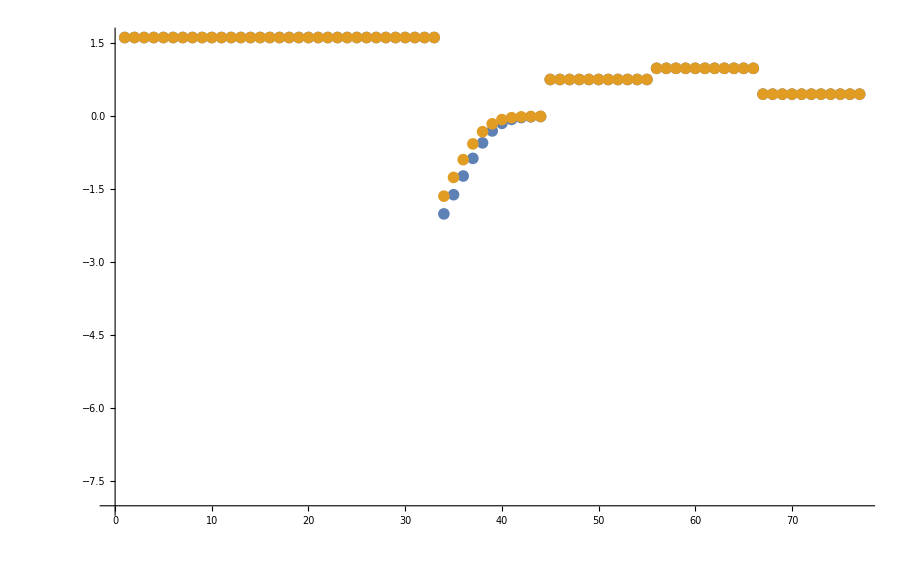

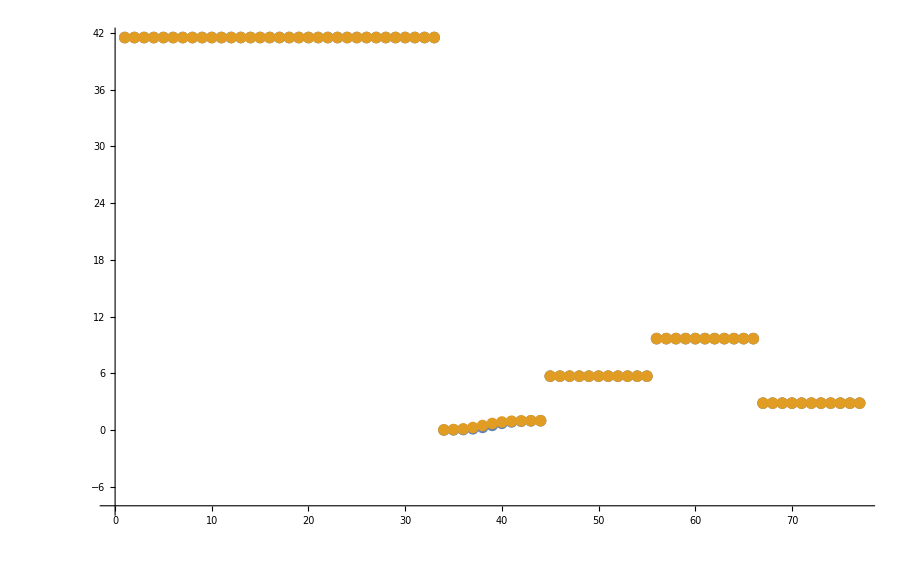

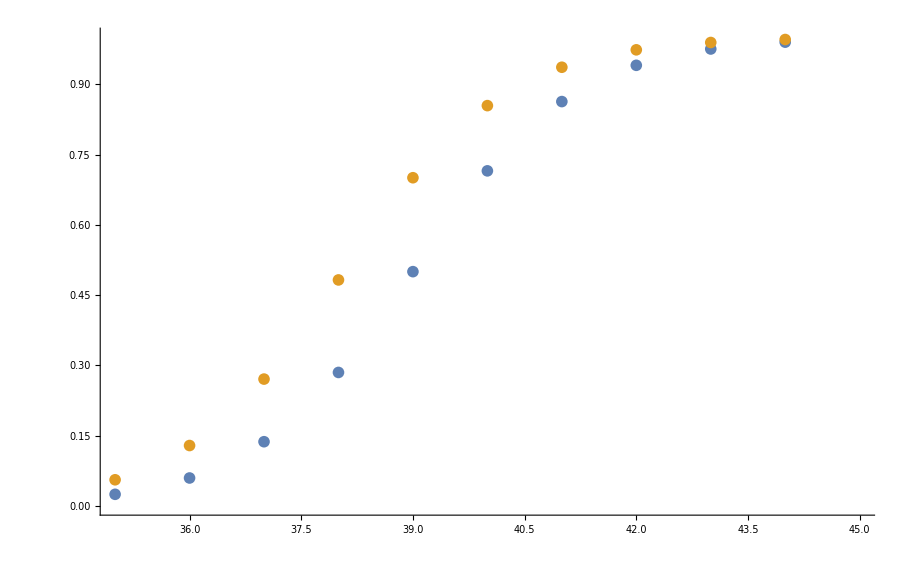

```mathematica
datasetI=5;
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[datasetI,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[datasetI,3]]}, AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]], filteredDataList[[datasetI,3]]}, AxesOrigin->{0,-8}, PlotRange->{{35,45}, {0,1}}]
```

```mathematica
enzymeModel["Reactions"]
```

{((PYK^c)_^+fdp^c⇌(PYK^c&fdp^c)_^)^PYK1,((PYK^c&pi^c)_^→(PYK^c)_^+pi^c)^PYK2,((PYK^c&fdp^c)_^+fdp^c⇌(PYK^c&fdp^c&fdp^c)_^)^PYK3,((PYK^c&pi^c&pi^c)_^→(PYK^c&pi^c)_^+pi^c)^PYK4,((PYK^c&fdp^c&fdp^c)_^→(PYK^c&pi^c&pi^c&f6p^c&f6p^c)_^)^PYK5,((PYK^c&pi^c&pi^c&f6p^c)_^→(PYK^c&pi^c&pi^c)_^+f6p^c)^PYK6,((PYK^c&pi^c&pi^c&f6p^c&f6p^c)_^→(PYK^c&pi^c&pi^c&f6p^c)_^+f6p^c)^PYK7}

### Parameter Distribution



```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```



```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```



```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```



```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=0.01;
paramSet = 1;
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, absoluteRateForward, absoluteRateReverse, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

data value | predicted value | error in %
0.000045 | 0.000045 | 1.21792×10^-9
0.00089 | 0.00089 | 1.07241×10^-9
0.00053 | 0.00053 | 1.84462×10^-9

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
268 | 268. | 5.51572×10^-10

```mathematica
backCalculateRatios[customRatiosDataList[[1]][[2]], customRatiosDataList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
425. | 425. | 3.88996×10^-10

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.408 | 0.408 | 4.88403×10^-10